Data from the sensor sheet and unit conversion

```mathematica
sensor ={{0.000, 0.0000},{50.000, 0.4049}, {100.000, 0.8093},{150.000, 1.2131}, {200.000, 1.6161}, {250.000, 2.0188}};
sensor[[All,1]] = UnitConvert[Quantity[sensor[[All,1]],"lb"], "g"];
sensor[[All,2 ]] = Quantity[sensor[[All,2]],"mV/V"] Quantity[10,"V"];
```

Data from the amplifier sheet

```mathematica
amplifierOutputMax = Quantity[10,"V"];
gain = Quantity[{0.5,1,1.5,2,2.5,3,4,10},"mV/V"];
```

Representing the impact of the gain choice

```mathematica
man = Manipulate[
afterGain = sensor;
afterGain[[All,2 ]] = sensor[[All,2 ]] /G;
beforeGain = sensor;
beforeGain[[All,2 ]] = UnitConvert[ sensor[[All,2 ]],"V"];
axesLabels = { "Weight (g)", "Voltage (V)"};

 ListPlot[{afterGain, beforeGain, {{80,amplifierOutputMax }} },AxesLabel-> axesLabels, PlotLabels-> {Style["After amplification",FontSize->Large],Style["Raw sensor",FontSize->Large],Style["Maximum (Force, Voltage)",FontSize->Large]}  ,
 PlotLabel->Style["Gain =  " <> ToString[ G],FontSize->Large], Joined-> {True, True, False},
ImageSize->Full,
LabelStyle->Bold],
{G,gain}]
```

## Validation trials

```mathematica
selectedGain = Quantity[2,"mV/V"];
calibrationData= sensor;
calibrationData[[All,2 ]] = sensor[[All,2 ]] /selectedGain;
lm = LinearModelFit[QuantityMagnitude[sensor],x,x];
```

```mathematica
Normal[lm]
```

0.00980952+0.000178025 x

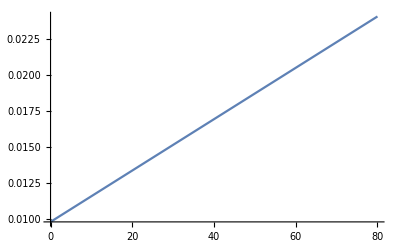

```mathematica
Plot[lm[x],{x,0,80}]
```

```mathematica
experimentName = {"NoLoad", "1kg","5kg", "6kg", "10kg","11kg","15kg","16kg"};
weights = Quantity[{1003, 5230,6233, 10013 , 11016,15243,16246},"g"];
filesNames= StringInsert[experimentName,".csv",-1];
filesNames = StringInsert[ files, NotebookDirectory[]<>"../Calibration/validationtrials/" , 1];
```

```mathematica
data = Table[Import[files[[x]],"Data"],{x,1,8}];
```

```mathematica
stickWeight = Mean[data[[1, 2000;; -10,47]]];
```

```mathematica
average = Table[Mean[data[[x,6;;-10, 47]]], {x,2,8}];
averagePoints = Table[{weights[[i]],average[[i]]},{i,1,7}];
```

```mathematica
expectedVoltage = lm /@ QuantityMagnitude[weights];
expectedVoltagePoints = Table [{ weights[[i]],expectedVoltage[[i]] + stickWeight},{i,1,7}];
```

```mathematica
ListPlot[  {average,expectedVoltage}, PlotLabels-> {"Measured", "Expected"},ImageSize->Large ]
```

-Graphics-

```mathematica
Manipulate[ListPlot[data[[x,6;;-10, 47]],ImageSize->Full,  PlotLabel->Style["Weight = " <> experimentName[[x]],FontSize->Large]], {x,1,8,1}]
```

Study of the Error

```mathematica
error = average - (expectedVoltage+ stickWeight)
```

{0.00714982,0.0339126,0.0783187,0.123488,0.128656,0.179002,0.191135}

```mathematica
weightError = Table[Solve[lm[x] == error[[y]]], {y, 1,7}]
```

{{{x→-14.94}},{{x→135.391}},{{x→384.829}},{{x→638.555}},{{x→667.584}},{{x→950.387}},{{x→1018.54}}}

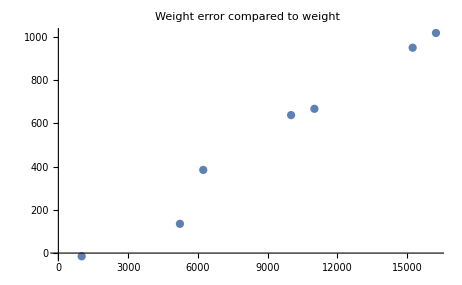

```mathematica
ListPlot[Table[{weights[[i]], Quantity[weightError[[i,1,1,2]],"g"]}, {i,1,7}], PlotLabel->"Weight error compared to weight" ]
```

```mathematica
Solve[lm[x] == stickWeight]
```

{{x→1609.48}}

```mathematica
NotebookDirectory[]
```

/mountain/tmeessen/Documents/ULB/ProjectAnkle/Master Project/Notebooks/

```mathematica
NotebookDirectory[]<>"../Calibration/validationtrials/1kg.csv"
```

/mountain/tmeessen/Documents/ULB/ProjectAnkle/Master Project/Notebooks/../Calibration/validationtrials/1kg.csv